```mathematica
(*All right. Our new goal is outlined in the following:
Let f:S->N be a function on an infinite set of integers S.Let k be in N.Then look at the sequence of numbers (N(f(m),m,f(m)+k))_{m=>1,m in S}.Does this sequence become constant when m is sufficiently large?If so,what number does the sequence converge to,and is there a nice formula for it?
*)
```

```mathematica
(* ================ MACROS / USER PARAMETERS =================*)
(* f:= our function of m on S to be evaluated; 
k := offset for n;
start:= first m to be checked in sequence. must be ≥ 1;
end:= last m to be checked in;
step := how much to increment by each iteration. determines what m are in our set S. 
e.g. step = 2 corresponds only even m.; *)
```

```mathematica
f[m_] := m/3; 
k = 25; 
start=4; 
end=50;
step = 2;

(* ====================================================== *)
```

```mathematica
(* Dependencies: *)
(* 
	Name: partitionN
 Mathematical Notation: N(r,m,n)
 Desc.: Gives the number of partitions of a positive integer, n, whose RANK is congruent to r, modulo m. 
*)

partitionN[r_,m_,n_]:=Module[{r0=r,m0=m,n0=n,counter=0,i,rank,list},
	list = IntegerPartitions[n0];
	Do[rank=Max[list[[i]]]-Length[list[[i]]]; 
	If[Mod[rank,m0]==r0,counter++]; ,{i,Length[list]}];
counter]
```

```mathematica
(* Build list. *)
```

```mathematica
dataList = {}
justVals = {}
For[i=start, i ≤ end, i+=step,
part = partitionN[f[i],i,f[i]+k];
AppendTo[justVals,part];
AppendTo[dataList, {i,f[i],part}]
];
```

{}

{}

```mathematica
(* Result (visuals): *)
```

```mathematica
Print[justVals]
```

{774,638,582,566,570,574,584,596,604,612,620,624,628,632,634,636,638,638,638}

```mathematica
(* Print[dataList]*)
```

{{4,2,774},{6,3,638},{8,4,582},{10,5,566},{12,6,570},{14,7,574},{16,8,584},{18,9,596},{20,10,604},{22,11,612},{24,12,620},{26,13,624},{28,14,628},{30,15,632},{32,16,634},{34,17,636},{36,18,638},{38,19,638},{40,20,638}}

{{4,2,6},{6,3,4},{8,4,4},{10,5,4},{12,6,4},{14,7,4},{16,8,4},{18,9,4},{20,10,4},{22,11,4},{24,12,4},{26,13,4},{28,14,4},{30,15,4},{32,16,4},{34,17,4},{36,18,4},{38,19,4},{40,20,4},{42,21,4},{44,22,4},{46,23,4},{48,24,4},{50,25,4},{52,26,4},{54,27,4},{56,28,4},{58,29,4},{60,30,4},{62,31,4},{64,32,4},{66,33,4},{68,34,4},{70,35,4}}

```mathematica
(* ListPointPlot3D[dataList]*)
```

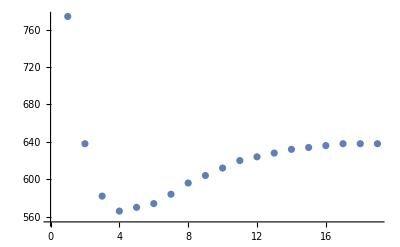

```mathematica
ListPlot[justVals]
```